```mathematica
importdata=Drop[Import["https://oku.edu.mie-u.ac.jp/~okumura/python/data/COVID-tokyo.csv"],23];
Last[importdata]
```

{2021-07-28,3177}

```mathematica
datasource="oku.edu.mie-u.ac.jp/~okumura/python/data/COVID-tokyo.csv";
font="Helvetica Neue";
startdate={2020,3,10};
enddate={2021,8,30};
tagoff=0.5;
startdateObj=DateObject[startdate];
date=4;
pos0={-3,7};radius=2Log[10]/Pi;tag={1,10,100,1000,10000,100000};tagtext={1,10,100,1000,10000,100000};
tagoff=0.5;

dataSmoothed=Table[{StringReplace[importdata[[i,1]],{"-"->"."}],
Mean[Table[importdata[[i-j,2]],{j,0,6}]]},{i,7,Length[importdata]}];data=DeleteCases[dataSmoothed,(x_)?(DateObject[#1[[1]]]<startdateObj&)];
minvalue=tag[[1]]/2;
maxvalue=3Last[tag];
```

```mathematica
stateOfemergency=
{{Position[data[[All,1]],"2020.04.07"][[1,1]],Position[data[[All,1]],"2020.05.25"][[1,1]]},{Position[data[[All,1]],"2021.01.07"][[1,1]],Position[data[[All,1]],"2021.03.21"][[1,1]]},
{Position[data[[All,1]],"2021.04.25"][[1,1]],Position[data[[All,1]],"2021.06.20"][[1,1]]},
{Position[data[[All,1]],"2021.07.12"][[1,1]],Length[data]}};
```

```mathematica
es[i_]:=
If[Total[Table[If[(i≥ stateOfemergency[[j,1]]&&i≤  stateOfemergency[[j,2]]),1,0],{j,1,4}]]>0,True,False];
```

```mathematica
slopeangle=Pi/4;
slopepos[val_,h_]:=pos0+{Cos[slopeangle]*val+h*Sin[slopeangle],(-Sin[slopeangle])*val+h*Cos[slopeangle]}
line[x_,val_]:=With[{angle=(val/Log[10])*Pi},{{x[[1]]+radius*Cos[-angle+Pi/2-slopeangle],x[[2]]+radius*Sin[-angle+Pi/2-slopeangle]},{x[[1]]-radius*Cos[-angle+Pi/2-slopeangle],x[[2]]-radius*Sin[-angle+Pi/2-slopeangle]}}];
```

```mathematica
uniformdist=Table[{2Random[]-1,2Random[]-1},{i,1,100000}];
infection=0.98radius Cases[uniformdist,x_?(Norm[#1]<1&)];
```

```mathematica
slope:=Show[Graphics[Table[Text[Style[tagtext[[i]],10,Black,FontFamily->font],slopepos[Log[tag[[i]]],-tagoff]],{i,1,Length[tag]}]],Graphics[Text[Style[0,10,Black,FontFamily->font],slopepos[Log[minvalue],0]+{-0.7,-0.2}]],Graphics[Line[{slopepos[Log[minvalue],0],slopepos[Log[maxvalue],0]}]],Graphics[Line[{slopepos[Log[minvalue],0],slopepos[Log[minvalue],0]-{10,0}}]],Graphics[Table[Line[{slopepos[Log[tag[[i]]],0],slopepos[Log[tag[[i]]],-0.2]}],{i,1,Length[tag]}]],Graphics[Table[Table[Line[{slopepos[Log[k*tag[[i]]],0],slopepos[Log[k*tag[[i]]],-0.1]}],{k,1,10}],{i,1,Length[tag]-1}]]];
```

```mathematica
title="Tokyo, new cases smoothed ";
fontsize=12;
```

```mathematica
ball[val_,i_]:=Module[{zeropx=-0.5,pos,ang,tpos,epos,dotnumber,dots},
Show[
If[val≤minvalue,
pos=slopepos[Log[minvalue],0]+{zeropx,radius};
ang=zeropx Cos[slopeangle]-Log[10]/4;
tpos=slopepos[Log[minvalue],0]+{zeropx,2.3radius},
pos=slopepos[Log[val],radius];
ang=Log[val];
tpos=slopepos[Log[val],2.3*radius]];
epos=slopepos[Log[val]+1.2radius,radius];
Graphics[{LightYellow,Opacity[1],EdgeForm[{Black,Thickness[Medium]}],Disk[pos,radius]}],
dotnumber=Round[val];
dots=Table[infection[[j]],{j,1,dotnumber}];
Graphics[Rotate[Table[{Red,Disk[pos+dots[[j]],0.02]},{j,1,dotnumber}],-ang/2,pos]],
Graphics[Rotate[Text[If[es[i],Style["緊急事態宣言",14,Red,Bold, FontFamily->font],""],epos],π/4,epos]]]]
```

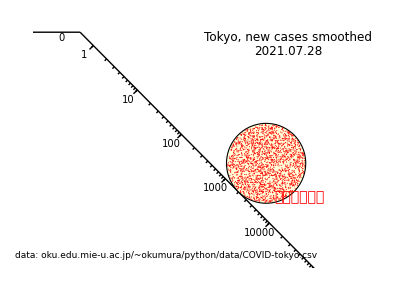
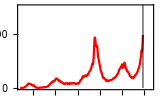

```mathematica
slopeangle=Pi/4;
tskip=0.5;
tx=pos0[[1]]+7.2;
ty=pos0[[2]]+0.3;
pltalldeath=DateListPlot[data[[All,2]]/.""->"0.",startdate,FrameStyle->Directive[9,Black,FontFamily->font],Frame->True,PlotStyle->Red,PlotRange->{{startdate,enddate},{0,3000}},ImageSize->160];
output=Table[plt=Show[pltalldeath,DateListPlot[{{DateObject[data[[i,1]]],0.0001},{DateObject[data[[i,1]]],10^7}},startdate,PlotStyle->{{Black,Thickness[0.004]}},Joined->True]];
Show[slope,ball[data[[i,2]],i],
Graphics[Inset[Graphics[plt],{-2,1.2}]],Graphics[Text[Style[title,fontsize,Black,FontFamily->font],{tx,ty}]],Graphics[Text[Style[data[[i,1]],fontsize,Black,FontFamily->font],{tx,ty-tskip}]],Graphics[Text[Style["data: "<>datasource,9,Black,FontFamily->font],{-0.3,-0.7}]],
PlotRange->{{-5,7},{-1,7.7}}],{i,1,Length[data]}];
outputMovie=Join[output,Table[Last[output],{j,1,30}]];

Last[outputMovie]
```

```mathematica
Export["~/Tokyo_new_cases.mp4",outputMovie]
```

~/Tokyo_new_cases.mp4